```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"];

<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
(*Plot[ Exp[-x^2/2], {x, -10, 10}, PlotRange->All]

f[k_, x_, R_] := NIntegrate[(1/2/k)Sin[k Abs[r]]Exp[-(x+ r)^2/2], {r, -R, R}]
Plot[f[1, x, 1000], {x, -100, 100}, PlotRange->All]*)
```

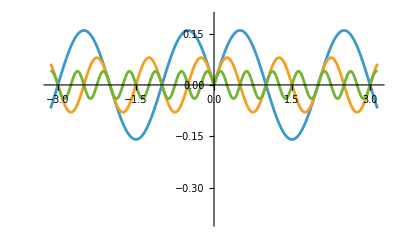

```mathematica
(*Plot[ Sin[Pi # Abs[r]]/(2# Pi) &/@ {1,2,4} //Evaluate, {r,  -Pi, Pi}, Ticks -> None]*)

ClearAll[plotOfOneDimGFig8]
plotOfOneDimGFig8 = Plot[Sin[Pi # Abs[r]]/(2 # Pi)&/@{1,2,4}//Evaluate,{r,-Pi,Pi},Ticks->None,PlotLegends->Placed[{
MaTeX["k = \\pi"],
MaTeX["k = 2 \\pi"],
MaTeX["k = 4 \\pi"]
},{Right,Bottom}],
PlotRange->{{-Pi, Pi}, {-0.4, 0.2}}]
```

```mathematica
peeters`exportForLatex["plotOfOneDimGFig8",plotOfOneDimGFig8]
```

{plotOfOneDimGFig8.eps,plotOfOneDimGFig8pn.png}